```mathematica
ExponentialExpand[listname_,function_,variable_,x0_,end_]:=Module[{},
Solve[Equal@@@Table[{Sum[listname[i]*D[Exp[-i*variable],{variable,k}]/.variable->x0,{i,0,end-1}],Evaluate[D[function,{variable,k}]]/.variable->x0},{k,0,end-1}],Table[listname[i],{i,0,end-1}]
]
];
```

```mathematica
Plot[Evaluate[Flatten[Table[serial[i],{i,0,19}]/.ExponentialExpand[serial,Log[x]/x,x,E,20]].Table[Exp[-i x],{i,0,19}]],{x,0.5,10},PlotRange->All]
```

$Aborted

```mathematica
?Equal
```

lhs==rhs returns True if lhs and rhs are identical.

```mathematica
D[f[x],{x,0}]
```

f[x]

```mathematica
ExponentialExpand[serial,Log[x]/x,x,1,20]//N
```

{{serial[0.]→0.332827,serial[1.]→1.40429,serial[2.]→-21.3469,serial[3.]→194.658,serial[4.]→-1565.95,serial[5.]→10048.8,serial[6.]→-52526.9,serial[7.]→225107.,serial[8.]→-796184.,serial[9.]→2.33176×10^6,serial[10.]→-5.65732×10^6,serial[11.]→1.13408×10^7,serial[12.]→-1.86694×10^7,serial[13.]→2.49795×10^7,serial[14.]→-2.67341×10^7,serial[15.]→2.23394×10^7,serial[16.]→-1.40395×10^7,serial[17.]→6.2388×10^6,serial[18.]→-1.74637×10^6,serial[19.]→231270.}}

```mathematica
CorrectedExponentialExpand[listname_,function_,variable_,x0_,end_]:=Module[{},
Solve[Equal@@@Table[{Sum[listname[i]*D[Exp[-i*variable],{variable,k}]/.variable->x0,{i,1,end}],Evaluate[D[function,{variable,k}]]/.variable->x0},{k,1,end}],Table[listname[i],{i,1,end}]
]
];
```

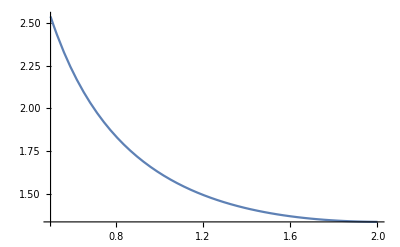

```mathematica
Plot[Evaluate[Flatten[Table[serial[i],{i,1,20}]/.CorrectedExponentialExpand[serial,x^-2,x,1,20]].Table[Exp[-i x],{i,0,19}]-x^-2],{x,0.5,2},PlotRange->All]
```

```mathematica
(Exp[-x^2-y^2+2x-2y+1]/.{Power->List,Times->List,Plus->List})[[2]]
```

{1,{2,x},{-1,{x,2}},{-2,y},{-1,{y,2}}}